```mathematica
ClearAll["Global`*"]
```

```mathematica
angle = {"000","010","020","030","040","050","060","070","080","090","100","110","120","130","140","150","160","170","180","190","200","210","220","230","240","250","260","270","280","290","300","310","320","330","340","350","360"};
```

```mathematica
myImportVH=Table[Reverse[Import["D:\\GraduateWork\\Dane\\Dodatkowe_dane\\15_05_18\\Ga2S3_VH\\"<>ang<>"_VH.txt","Table"][[2;;-1]]],{ang,angle}];
```

```mathematica
f[data_]:=Sort[data,#1[[1]]<#2[[1]]&];
```

```mathematica
(*Wszystkie piki*)
```

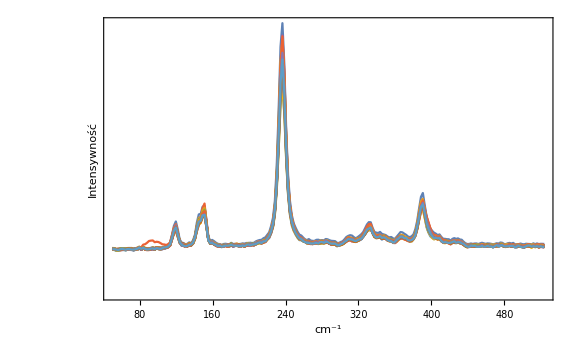

```mathematica
plotAllVH=ListPlot[Table[f[myImportVH[[i]]][[120;;350]],{i,1,37,1}], Joined->True,PlotRange->Full,Frame->True,FrameTicks->  {{False,False},{True,False}},FrameLabel->{Style["cm^-1",Bold,12,Black],Style["Intensywność",Bold,12,Black]},ImageSize->Large]
```

```mathematica
myImportVV=Table[Reverse[Import["D:\\GraduateWork\\Dane\\Dodatkowe_dane\\15_05_18\\Ga2S3_VV\\"<>ang<>"_VV.txt","Table"][[2;;-1]]],{ang,angle}];
```

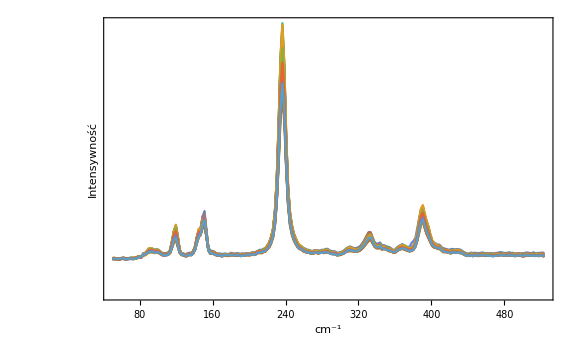

```mathematica
plotAllVV=ListPlot[Table[f[myImportVV[[i]]][[120;;350]],{i,1,37,1}], Joined->True,PlotRange->Full,Frame->True,FrameTicks->  {{False,False},{True,False}},FrameLabel->{Style["cm^-1",Bold,12,Black],Style["Intensywność",Bold,12,Black]},ImageSize->Large]
```

```mathematica
(*Jeden pik*)
```

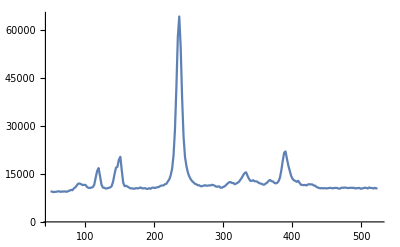

```mathematica
ListPlot[f[myImportVV[[10]]][[120;;350]], Joined->True,PlotRange->Full]
```

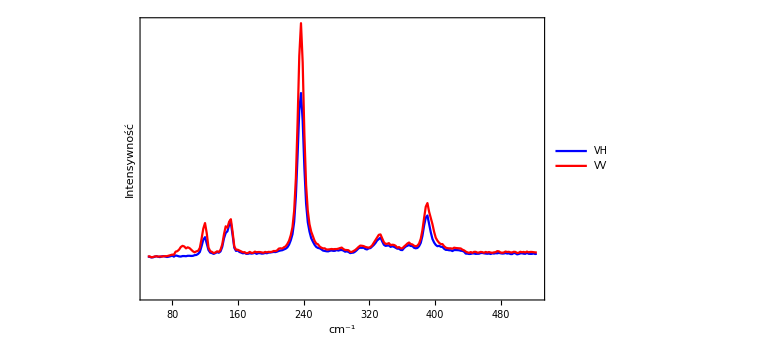

```mathematica
plotVVandVH=ListPlot[{f[myImportVH[[15]]][[120;;350]],f[myImportVV[[15]]][[120;;350]]}, PlotLegends->Placed[{"VH","VV"},Above],
PlotStyle->{Directive[Blue],Directive[Red]},Joined->True,PlotRange->Full,Frame->True,FrameTicks->  {{False,False},{True,False}},FrameLabel->{Style["cm^-1",Bold,12,Black],Style["Intensywność",Bold,12,Black]},ImageSize->Large]
```

```mathematica
Export["D:\\GraduateWork\\Opracowanie\\script_spectre\\plotAllVH.pdf",plotAllVH,"PDF"]
Export["D:\\GraduateWork\\Opracowanie\\script_spectre\\plotAllVV.pdf",plotAllVV,"PDF"]
Export["D:\\GraduateWork\\Opracowanie\\script_spectre\\plotVVandVH.png",plotVVandVH,"PNG"]
```

D:\GraduateWork\Opracowanie\script_spectre\plotAllVH.pdf

D:\GraduateWork\Opracowanie\script_spectre\plotAllVV.pdf

D:\GraduateWork\Opracowanie\script_spectre\plotVVandVH.png

```mathematica
(*GaP z Ga2S3 514 nm*)
```

```mathematica
daneGaP=Import["D:\\GraduateWork\\Dane\\Dodatkowe_dane\\raman_inne_probki\\GaP-wzorzec-514nm-01.txt","Table"][[2;;-1]];
```

```mathematica
goodDaneGaP=f[daneGaP];
```

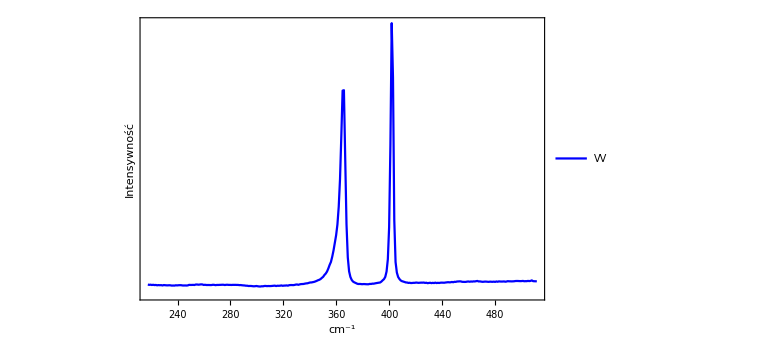

```mathematica
plotGaP=ListPlot[goodDaneGaP[[200;;500]],PlotLegends->Placed[{"VV"},Above],
PlotStyle->{Directive[Blue],Directive[Red]},Joined->True,PlotRange->Full,Frame->True,FrameTicks->  {{False,False},{True,False}},FrameLabel->{Style["cm^-1",Bold,12,Black],Style["Intensywność",Bold,12,Black]},ImageSize->Large]
```

```mathematica
daneGa2S3GaP=Import["D:\\GraduateWork\\Dane\\Dodatkowe_dane\\Data_1\\SLA39-514nm--pytkiGa2S3.txt","Table"][[2;;-1]];
```

```mathematica
goodDaneGa2S3GaP = f[daneGa2S3GaP];
```

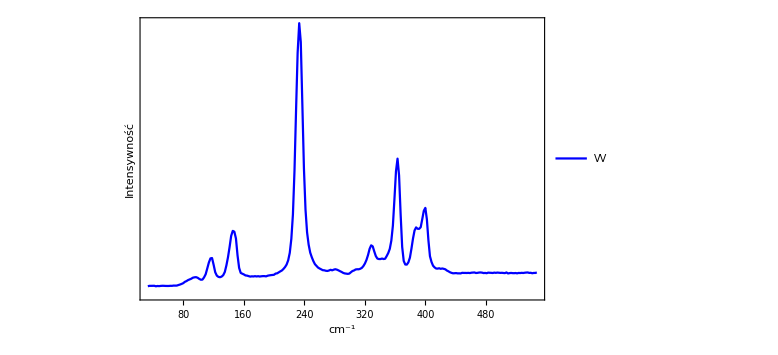

```mathematica
plotGapWithGa2S3=ListPlot[goodDaneGa2S3GaP[[1;;250]],PlotLegends->Placed[{"VV"},Above],
PlotStyle->{Directive[Blue],Directive[Red]},Joined->True,PlotRange->Full,Frame->True,FrameTicks->  {{False,False},{True,False}},FrameLabel->{Style["cm^-1",Bold,12,Black],Style["Intensywność",Bold,12,Black]},ImageSize->Large]
```

```mathematica
Export["D:\\GraduateWork\\Opracowanie\\script_spectre\\plotGaP.png",plotGaP,"PNG"]
Export["D:\\GraduateWork\\Opracowanie\\script_spectre\\plotGapWithGa2S3.png",plotGapWithGa2S3,"PNG"]
```

D:\GraduateWork\Opracowanie\script_spectre\plotGaP.png

D:\GraduateWork\Opracowanie\script_spectre\plotGapWithGa2S3.png